# 矩阵

## 克罗内克积

```mathematica
String2Pic[string_]:=Rasterize[Text[string],RasterSize->100,ImageSize->50](*将符号转化为图片*)
```

```mathematica
KroneckerMatrixPlot[matrixA_,matrixB_]:=Module[{plots},
plots=MatrixPlot[#,PlotTheme->"Minimal"]&/@{matrixA,matrixB,KroneckerProduct[matrixA,matrixB]};
Row[{plots[[1]],String2Pic["⊗"],plots[[2]],String2Pic["="],plots[[3]]}]
]
```

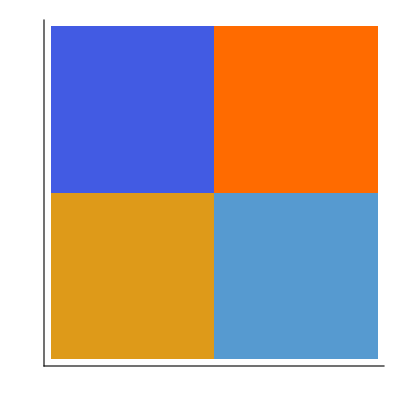
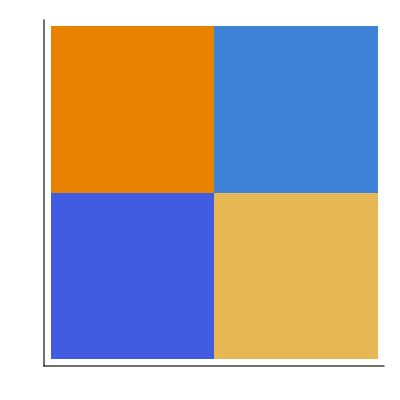
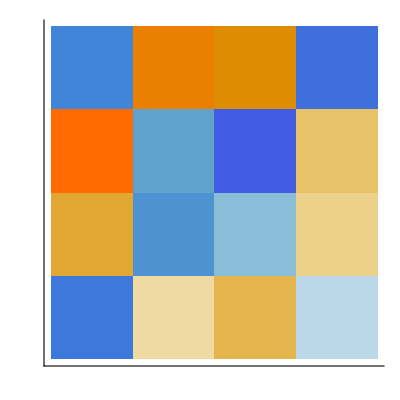
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
A={{-1,1},{0.7,-0.4}};
B={{0.5,-0.6},{-0.8,0.3}};
KroneckerMatrixPlot[A,B]
```

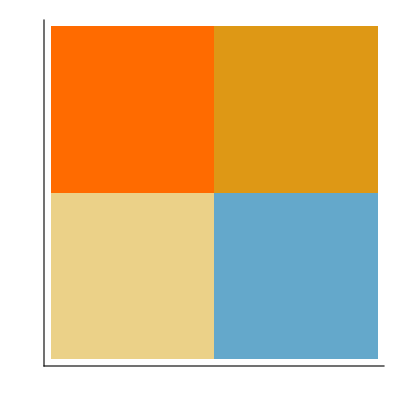
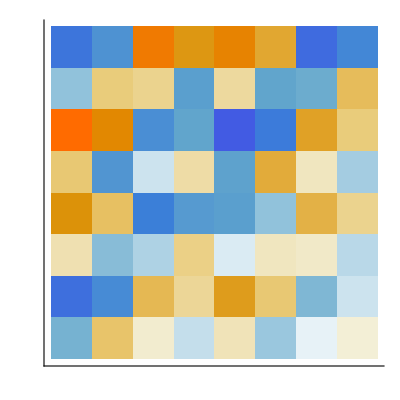
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
CC={{0.9,0.5},{0.2,-0.3}};
KroneckerMatrixPlot[KroneckerProduct[A,B],CC]
```

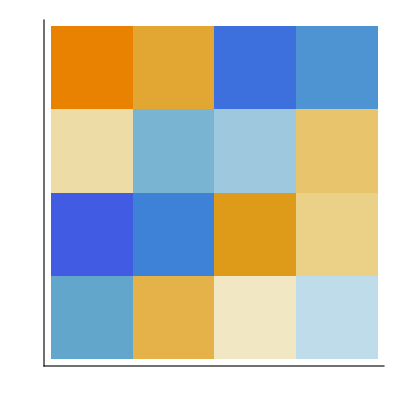
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
KroneckerMatrixPlot[A,KroneckerProduct[B,CC]](*满足结合律*)
```